```mathematica
GMC = 1.84217;
```

```mathematica
Solve[{
s1x ==-0.3860653 s0x+0.3020571 s0a-0.5674127 GMC δ, s1a ==  -0.7171161 s0x-2.029164 s0a-0.2587972 GMC δ, L == 0.3069881 s0x  + 1.229545 s0a + 1.687310 GMC δ }, {L, δ, s1a}]
```

{{L→2.12777 s0a-0.841051 s0x-2.97369 s1x,δ→0.288975 s0a-0.369345 s0x-0.95669 s1x,s1a→-2.16693 s0a-0.541032 s0x+0.4561 s1x}}

```mathematica
Solve[{
s1x/1000 ==-0.3860653 s0x/1000+0.3020571 s0a-0.5674127 GMC δ, s1a ==  -0.7171161 s0x/1000-2.029164 s0a-0.2587972 GMC δ, L/1000 == 0.3069881 s0x/1000  + 1.229545 s0a + 1.687310 GMC δ }, {L, δ, s1a}]
```

{{L→2127.77 s0a-0.841051 s0x-2.97369 s1x,δ→0.288975 s0a-0.000369345 s0x-0.00095669 s1x,s1a→-2.16693 s0a-0.000541032 s0x+0.0004561 s1x}}

```mathematica
x2[s0x_,s0a_,s0y_,s0b_,δ_]:=-0.3860653 s0x + 0.3020571 s0a - 0.5674127 δ -12.3748 s0x^2-75.69397 s0x s0a - 116.1523 s0a^2 + 1.279556 s0y^2+ 5.263761 s0y s0b + 2.43888 s0x δ +8.100786 s0a δ + 10.24653 s0b^2+0.3927182  δ^2
a2[s0x_,s0a_,s0y_,s0b_,δ_]:= -0.7171161 s0x - 2.029164 s0a -0.2587972  δ-1.313666 s0x^2-8.461706 s0x s0a +0.1186313 s0y^2-0.1737277 s0y s0b + 0.2551363 s0x δ  + 2.028798 s0a δ + 0.03594439 s0b^2+0.03150458 δ^2
y2[s0x_,s0a_,s0y_,s0b_,δ_]:= -3.838873 s0y - 0.9557328 s0b + 12.08177 s0x s0y + 35.77021 s0a s0y + 52.63741 s0x s0b + 149.5601 s0a s0b+ 3.949952 s0y δ  + 8.983404 s0b δ 
b2[s0x_,s0a_,s0y_,s0b_,δ_]:= -1.133071 s0y -0.5425847 s0b + 3.406991 s0x s0y 9.186467 s0a s0y+ 14.53556 s0a s0b+0.5552344 s0y δ + 2.231465 s0b δ 
L2[s0x_,s0a_,s0y_,s0b_,δ_]:= 0.3069881 s0x + 1.229545 s0a + 1.687310  δ -3.282403 s0x^2-19.81407 s0x s0a-30.91472 s0a^2-0.9082193 s0y^2-0.1517058 s0y s0b -0.05251553 s0x δ -0.6675170 s0a δ + 1.260591 s0b^2-1.388244 δ^2
```

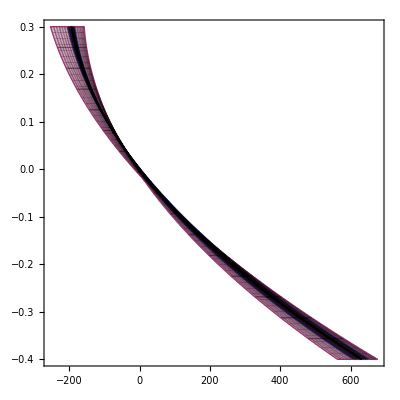

```mathematica
ParametricPlot[{
{x2[s0a,0,0,0,GMC δ]1000,δ},
{x2[0,s0a,0,0,GMC δ]1000,δ},
{x2[0,0,0,0,GMC δ]1000,δ}
},{s0a,-0.01,0.01},{δ,-0.4,0.3},AspectRatio->1]
```

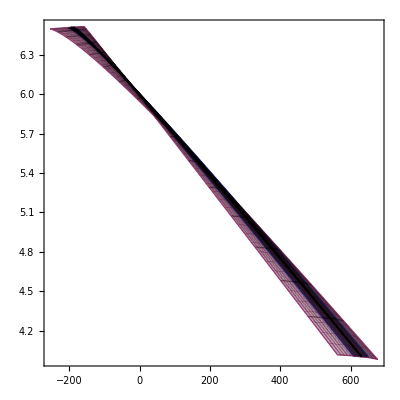

```mathematica
ParametricPlot[{
{x2[s0a,0,0,0,GMC δ]1000,L2[s0a,0,0,0,GMC δ]+6},
{x2[0,s0a,0,0,GMC δ]1000,L2[0,s0a,0,0,GMC δ]+6},
(*{x2[0,0,s0a,0,GMC δ]1000,L2[0,0,s0a,0,GMC δ]+6},*)
(*{x2[0,0,0,s0a,GMC δ]1000,L2[0,0,0,s0a,GMC δ]+6},*)
{x2[0,0,0,0,GMC δ]1000,L2[0,0,0,0,GMC δ]+6}
},{s0a,-0.01,0.01},{δ,-0.4,0.3},AspectRatio->1]
```

```mathematica
DataXL=Table[{x[0,0,0,0,δ]1000,LL[0,0,0,0,δ]+6}, {δ, -0.4,0.3,0.01}];
DataXδ=Table[{x[0,0,0,0,δ]1000,δ}, {δ, -0.4,0.3,0.01}];
```

## 3rd order

```mathematica
ME={
{-0.3860653,-0.7171161, 0.000000, 0.000000, 0.3069881, "100000"},
{0.3020571,-2.029164, 0.000000, 0.000000, 1.229545, "010000"},
{0.000000,0.000000,-3.838873,-1.133071 ,0.000000, "001000"},
{0.000000, 0.000000,-0.9557328,-0.5425847, 0.000000, "000100"},
{0.000000, 0.000000, 0.000000, 0.000000, 1.000000, "000010"},
{-0.5674127,-0.2587972, 0.000000, 0.000000, 1.687310, "000001"},
{-12.37480,-1.313666, 0.000000, 0.000000,-3.282403, "200000"},
{-75.69397,-8.461706, 0.000000, 0.000000,-19.81407, "110000"},
{-116.1523,-13.51837, 0.000000, 0.000000,-30.91472, "020000"},
{0.000000, 0.000000, 13.08177, 3.406991, 0.000000, "101000"},
{0.000000, 0.000000, 35.77021, 9.186467, 0.000000, "011000"},
{1.279556, 0.1186313, 0.000000, 0.000000,-0.9082193, "002000"},
{0.000000, 0.000000, 52.63741, 14.53556, 0.000000, "100100"},
{0.000000, 0.000000, 149.5601, 41.37510, 0.000000,"010100"},
{5.263761,-0.1737277, 0.000000, 0.000000,-0.1517058, "001100"},
{2.438880, 0.2551363, 0.000000, 0.000000,-0.05251553, "100001"},
{8.100786, 2.028798, 0.000000, 0.000000,-0.6675170, "010001"},
{0.000000, 0.000000, 3.949952, 0.5552344, 0.000000, "001001"},
{10.24653, 0.03594439, 0.000000, 0.000000, 1.260591, "000200"},
{0.000000, 0.000000, 8.983404, 2.231465, 0.000000, "000101"},
{0.3927182, 0.03150458, 0.000000, 0.000000,-1.388244, "000002"},
{144.1968, 18.77961, 0.0, 0.0, 24.41648, "300000"},
{1326.537, 173.5901, 0.0, 0.0, 225.1670, "210000"},
{4073.270, 534.1469, 0.0, 0.0, 693.8006, "120000"},
{4173.729, 546.7909, 0.0, 0.0, 714.6225, "030000"},
{0.0, 0.0,-121.3224,-31.81902, 0.0, "201000"},
{0.0, 0.0,-678.5772,-175.7929, 0.0, "111000"},
{0.0, 0.0,-967.3620,-248.0481, 0.0, "021000"},
{-23.94647,-3.700989,0,0, 0.9504601, "102000"},
{-72.76142,-10.78221,0,0 ,2.442925, "012000"},
{0.0,0.0, 7.041744, 5.054322,0.0, "003000"},
{0.0,0.0,-627.3093,-173.1116 ,0.0, "200100"},
{0.0, 0.0,-3687.462,-1018.499 ,0.0 ,"110100"},
{0.0, 0.0,-5472.768,-1512.726, 0.0, "020100"},
{-143.7400,-8.544729, 0.0, 0.0,-4.352987, "101100"},
{-421.1660,-32.24846,0.0, 0.0,-13.19333, "011100"},
{0.0,0.0, 127.5200, 37.98650,0.0, "002100"},
{9.077397,-0.3460173 ,0.000000, 0.000000, 4.147680, "200001"},
{94.67025, 2.606426, 0.000000, 0.000000, 34.93084, "110001"},
{204.3910, 11.09139, 0.000000, 0.000000, 68.86251, "020001"},
{0.000000 ,0.000000,-2.250960 ,0.3712736, 0.000000, "101001"},
{0.000000, 0.000000,-18.93223,-1.119100 ,0.000000, "011001"},
{0.8364735,-1.415303, 0.000000, 0.000000, 2.449331, "002001"},
{-290.6730,-19.41340 ,0.0, 0.0,-49.96967, "100200"},
{-873.0898,-68.59175 ,0.0, 0.0,-149.2290, 010200},
{0.0,0.0, 368.9242, 99.71493,-0.5738863E-14, 001200},
{0.000000, 0.000000,-51.26994,-7.747725, 0.000000, 100101},
{0.000000 ,0.000000,-218.8943,-41.97511 ,0.000000 ,010101},
{2.642794 ,0.7507463 ,0.000000, 0.000000, 6.487740, 001101},
{-2.665078,-0.1475240 ,0.000000 ,0.000000 ,0.1128635, 100002},
{-12.38477,-1.418634, 0.000000, 0.000000, 0.7451535, 010002},
{0.000000, 0.000000,-4.157363,-0.8578950, 0.000000, 001002},
{0.0, 0.0, 376.0054, 102.2166, 0.0, 000300},
{-0.2817120 ,2.377927, 0.000000, 0.000000, 2.666954, 000201},
{0.000000 ,0.000000,-13.03858,-2.477693, 0.000000, 000102},{-0.3330673,-0.03833033, 0.000000, 0.000000, 1.189690, 000003}};
```

```mathematica
vector={s0x, s0a, s0y, s0b, 6, δ, s0x^2, s0x s0a, s0a^2, s0x s0y, s0a s0y, s0y^2, s0x s0b, s0a s0b, s0y s0b, s0x δ, s0a δ, s0y δ, s0b^2, s0b δ, δ^2, s0x^3, s0x^2 s0a, s0x s0a^2, s0a^3, s0x^2 s0y, s0x s0a s0y, s0a^2 s0y, s0x s0y^2, s0a s0y^2, s0y^3, s0x^2 s0b, s0x s0a s0b, s0a^2 s0b, s0x s0y s0b, s0a s0y s0b, s0y^2 s0b, s0x^2 δ, s0x s0a δ, s0a^2 δ, s0x s0y δ, s0a s0y δ, s0y^2 δ, s0x s0b^2, s0a s0b^2, s0y s0b^2, s0x s0b δ, s0a s0b δ, s0y s0b δ, s0x δ^2, s0a δ^2, s0y δ^2, s0b^3, s0b^2 δ, s0b δ^2, δ^3};
```

```mathematica
(Transpose[ME].vector)[[2]]
```

0.-2.02916 s0a-13.5184 s0a^2+546.791 s0a^3+0.0359444 s0b^2-68.5918 s0a s0b^2-0.717116 s0x-8.46171 s0a s0x+534.147 s0a^2 s0x-19.4134 s0b^2 s0x-1.31367 s0x^2+173.59 s0a s0x^2+18.7796 s0x^3-0.173728 s0b s0y-32.2485 s0a s0b s0y-8.54473 s0b s0x s0y+0.118631 s0y^2-10.7822 s0a s0y^2-3.70099 s0x s0y^2-0.258797 δ+2.0288 s0a δ+11.0914 s0a^2 δ+2.37793 s0b^2 δ+0.255136 s0x δ+2.60643 s0a s0x δ-0.346017 s0x^2 δ+0.750746 s0b s0y δ-1.4153 s0y^2 δ+0.0315046 δ^2-1.41863 s0a δ^2-0.147524 s0x δ^2-0.0383303 δ^3

```mathematica
X[s0x_,s0a_,s0y_,s0b_,δ_]:=0.+0.3020571 s0a-116.1523 s0a^2+4173.729 s0a^3+10.24653 s0b^2-873.0898 s0a s0b^2-0.3860653 s0x-75.69397 s0a s0x+4073.27 s0a^2 s0x-290.673 s0b^2 s0x-12.3748 s0x^2+1326.537 s0a s0x^2+144.1968 s0x^3+5.263761 s0b s0y-421.166 s0a s0b s0y-143.74 s0b s0x s0y+1.279556 s0y^2-72.76142 s0a s0y^2-23.94647 s0x s0y^2-0.5674127 δ+8.100786 s0a δ+204.391 s0a^2 δ-0.281712 s0b^2 δ+2.43888 s0x δ+94.67025 s0a s0x δ+9.077397 s0x^2 δ+2.642794 s0b s0y δ+0.8364735 s0y^2 δ+0.3927182 δ^2-12.38477 s0a δ^2-2.665078 s0x δ^2-0.3330673 δ^3
A[s0x_,s0a_,s0y_,s0b_,δ_]:=0.-2.029164 s0a-13.51837 s0a^2+546.7909 s0a^3+0.03594439 s0b^2-68.59175 s0a s0b^2-0.7171161 s0x-8.461706 s0a s0x+534.1469 s0a^2 s0x-19.4134 s0b^2 s0x-1.313666 s0x^2+173.5901 s0a s0x^2+18.77961 s0x^3-0.1737277 s0b s0y-32.24846 s0a s0b s0y-8.544729 s0b s0x s0y+0.1186313 s0y^2-10.78221 s0a s0y^2-3.700989 s0x s0y^2-0.2587972 δ+2.028798 s0a δ+11.09139 s0a^2 δ+2.377927 s0b^2 δ+0.2551363 s0x δ+2.606426 s0a s0x δ-0.3460173 s0x^2 δ+0.7507463 s0b s0y δ-1.415303 s0y^2 δ+0.03150458 δ^2-1.418634 s0a δ^2-0.147524 s0x δ^2-0.03833033 δ^3
B[s0x_,s0a_,s0y_,s0b_,δ_]:=0.-0.5425847 s0b+41.3751 s0a s0b-1512.726 s0a^2 s0b+102.2166 s0b^3+14.53556 s0b s0x-1018.499 s0a s0b s0x-173.1116 s0b s0x^2-1.133071 s0y+9.186467 s0a s0y-248.0481 s0a^2 s0y+99.71493 s0b^2 s0y+3.406991 s0x s0y-175.7929 s0a s0x s0y-31.81902 s0x^2 s0y+37.9865 s0b s0y^2+5.054322 s0y^3+2.231465 s0b δ-41.97511 s0a s0b δ-7.747725 s0b s0x δ+0.5552344 s0y δ-1.1191 s0a s0y δ+0.3712736 s0x s0y δ-2.477693 s0b δ^2-0.857895 s0y δ^2
Y[s0x_,s0a_,s0y_,s0b_,δ_]:=0.-0.9557328 s0b+149.5601 s0a s0b-5472.768 s0a^2 s0b+376.0054 s0b^3+52.63741 s0b s0x-3687.462 s0a s0b s0x-627.3093 s0b s0x^2-3.838873 s0y+35.77021 s0a s0y-967.362 s0a^2 s0y+368.9242 s0b^2 s0y+13.08177 s0x s0y-678.5772 s0a s0x s0y-121.3224 s0x^2 s0y+127.52 s0b s0y^2+7.041744 s0y^3+8.983404 s0b δ-218.8943 s0a s0b δ-51.26994 s0b s0x δ+3.949952 s0y δ-18.93223 s0a s0y δ-2.25096 s0x s0y δ-13.03858 s0b δ^2-4.157363 s0y δ^2
LL[s0x_,s0a_,s0y_,s0b_,δ_]:=1.229545 s0a-30.91472 s0a^2+714.6225 s0a^3+1.260591 s0b^2-149.229 s0a s0b^2+0.3069881 s0x-19.81407 s0a s0x+693.8006 s0a^2 s0x-49.96967 s0b^2 s0x-3.282403 s0x^2+225.167 s0a s0x^2+24.41648 s0x^3-0.1517058 s0b s0y-13.19333 s0a s0b s0y-15.559984700891595 s0b^2 s0y-4.352987 s0b s0x s0y-0.9082193 s0y^2+2.442925 s0a s0y^2+0.9504601 s0x s0y^2+1.68731 δ-0.667517 s0a δ+68.86251 s0a^2 δ+2.666954 s0b^2 δ-0.05251553 s0x δ+34.93084 s0a s0x δ+4.14768 s0x^2 δ+6.48774 s0b s0y δ+2.449331 s0y^2 δ-1.388244 δ^2+0.7451535 s0a δ^2+0.1128635 s0x δ^2+1.18969 δ^3
```

```mathematica
Y[s0a,0,0,0,GMC δ]
Y[0,s0a,0,0,GMC δ]
Y[0,0,s0a,0,GMC δ]
Y[0,0,0,s0a,GMC δ]
Y[0,0,0,0,GMC ]
```

0.

0.

0.-3.83887 s0a+7.04174 s0a^3+7.27648 s0a δ-14.1084 s0a δ^2

0.-0.955733 s0a+376.005 s0a^3+16.549 s0a δ-44.2476 s0a δ^2

0.

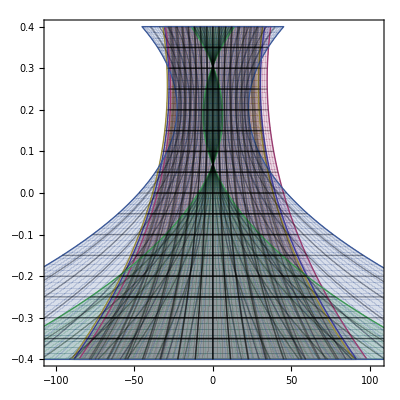

```mathematica
ParametricPlot[{
{Y[s0a,0,s0a,0,GMC δ]1000,δ},
{Y[s0a,s0a,s0a,0,GMC δ]1000,δ},
{Y[0,0,s0a,0,GMC δ]1000,δ},
{Y[0,0,0,s0a,GMC δ]1000,δ},
{Y[0,0,s0a,s0a,GMC δ]1000,δ}
},{s0a,-0.01,0.01},{δ,-0.4,0.4},AspectRatio->1]
```

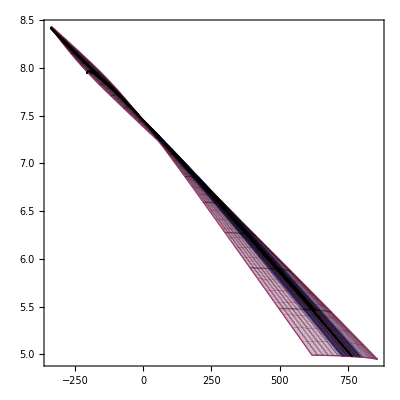

```mathematica
ParametricPlot[{
{X[s0a,0,0,0,GMC δ]1000,LL[s0a,0,0,0,GMC δ]+7.45226},
{X[0,s0a,0,0,GMC δ]1000,LL[0,s0a,0,0,GMC δ]+7.45226},
{X[0,0,s0a,0,GMC δ]1000,LL[0,0,s0a,0,GMC δ]+7.45226},
(*{X[0,0,0,s0a,GMC δ]1000,LL[0,0,0,s0a,GMC δ]},*)
{X[0,0,0,0,GMC δ]1000,LL[0,0,0,0,GMC δ]+7.45226},
{x2[0,0,0,0,GMC δ]1000,L2[0,0,0,0,GMC δ]+7.45226}
},{s0a,-0.01,0.01},{δ,-0.4,0.4},AspectRatio->1]
```

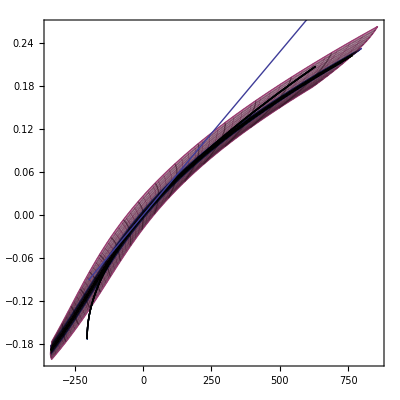

```mathematica
Show[
{ParametricPlot[{
{X[s0a,0,0,0,GMC δ]1000,A[s0a,0,0,0,GMC δ]},
{X[0,s0a,0,0,GMC δ]1000,A[0,s0a,0,0,GMC δ]},
{X[0,0,s0a,0,GMC δ]1000,A[0,0,s0a,0,GMC δ]},
{X[0,0,0,0,GMC δ]1000,A[0,0,0,0,GMC δ]},
{x2[0,0,0,0,GMC δ]1000,a2[0,0,0,0,GMC δ]}
},{s0a,-0.01,0.01},{δ,-0.4,0.4},AspectRatio->1],
ParametricPlot[
{s1x 1000,(-2.1669323857272142 0-0.5410315346436729 0+0.45610047149103294 s1x)},{s1x,-0.2, 0.8}]}
]
```

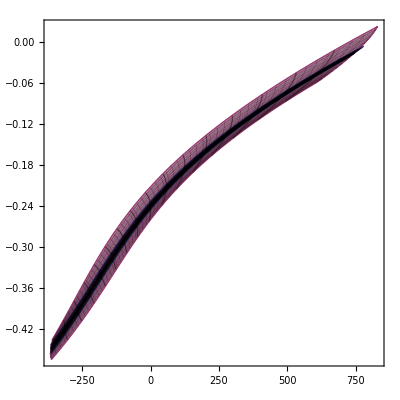

```mathematica
ParametricPlot[{
Rot[X[s0a,0,0,0,GMC δ]1000,A[s0a,0,0,0,GMC δ],0,0,13.5°][[{1,2}]],
Rot[X[0,s0a,0,0,GMC δ]1000,A[0,s0a,0,0,GMC δ],0,0,13.5°][[{1,2}]],
Rot[X[0,0,0,0,GMC δ]1000,A[0,0,0,0,GMC δ],0,0,13.5°][[{1,2}]]
},{s0a,-0.01,0.01},{δ,-0.4,0.4},AspectRatio->1]
```

```mathematica
Rot[x_,a_,y_,b_,θ_]:={x 1/(a Sin[θ]+Cos[θ]), (a Cos[θ]-Sin[θ])/(a Sin[θ]+Cos[θ]),y-b x Sin[θ]/(a Sin[θ]+Cos[θ]), b/(a Sin[θ]+Cos[θ]) }
```

```mathematica
Rot[1,0,0,0,45°]
```

{√2,-1,0,0}

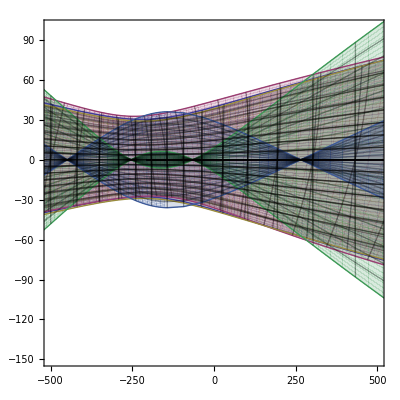

```mathematica
ParametricPlot[{
{X[s0a,0,s0a,0,GMC δ]1000,Y[s0a,0,s0a,0,GMC δ]1000},
{X[0,s0a,s0a,0,GMC δ]1000,Y[0,s0a,s0a,0,GMC δ]1000},
{X[0,0,s0a,0,GMC δ]1000,Y[0,0,s0a,0,GMC δ]1000},
{X[0,0,0,s0a,GMC δ]1000,Y[0,0,0,s0a,GMC δ]1000},
{X[0,0,s0a,-s0a,GMC δ]1000,Y[0,0,s0a,-s0a,GMC δ]1000},
{x2[0,0,0,0,GMC δ]1000,y2[0,0,0,0,GMC δ]1000}
},{s0a,-0.01,0.01},{δ,-0.4,0.6},PlotRange->{{-500,500},{-150,100}},AspectRatio->1]
```

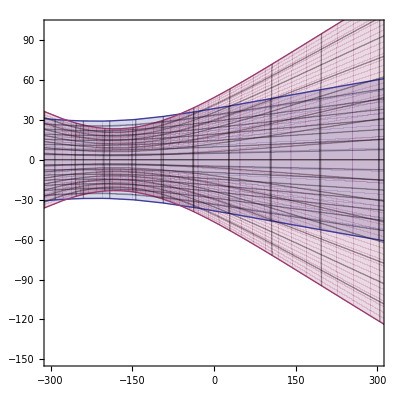

```mathematica
ParametricPlot[{
{X[0,0,s0a,0,GMC δ]1000,Y[0,0,s0a,0,GMC δ]1000},
Rot[X[0,0,s0a,s0a,GMC δ]1000,A[0,0,s0a,s0a,GMC δ],Y[0,0,s0a,s0a,GMC δ]1000,B[0,0,s0a,s0a,GMC δ],13.5°][[{1,3}]]
},{s0a,-0.01,0.01},{δ,-0.4,0.6},PlotRange->{{-300,300},{-150,100}},AspectRatio->1]
```

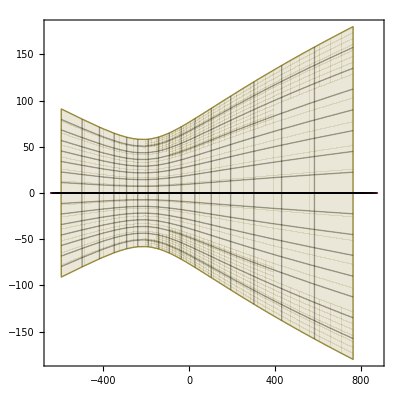

```mathematica
ParametricPlot[{
{X[s0a,s0a,0,0,GMC δ]1000,Y[s0a,0,0,0,GMC δ]1000},
{X[0,s0a,0,0,GMC δ]1000,Y[0,s0a,0,0,GMC δ]1000},
{X[0,0,s0a,0,GMC δ]1000,Y[0,0,s0a,0,GMC δ]1000},
{X[0,0,0,0,GMC δ]1000,Y[0,0,0,0,GMC δ]1000},
{x2[0,0,0,0,GMC δ]1000,y2[0,0,0,0,GMC δ]1000}
},{s0a,-0.02,0.02},{δ,-0.4,0.6},AspectRatio->1]
```

```mathematica
DataXL=Table[{X[0,0,0,0,GMC δ]1000,LL[0,0,0,0,GMC δ]+6}, {δ, -0.4,0.4,0.01}];
DataXδ=Table[{X[0,0,0,0,GMC δ]1000,δ}, {δ, -0.4,0.4,0.01}];
DataXA=Table[{X[0,0,0,0,GMC δ]1000,A[0,0,0,0,GMC δ]}, {δ, -0.4,0.4,0.01}];
```

```mathematica
Remove[q0,q1,q2,q3]
{j0,j1,j2}={q0,q1,q2}/.FindFit[DataXL,q0+ q1 x+q2 x^2,{q0,q1,q2},x]
{p0,p1,p2,p3}={q0,q1,q2,q3}/.FindFit[DataXL,q0+ q1 x+q2 x^2+q3 x^3 ,{q0,q1,q2,q3},x]
Sum[h=DataXL[[i,1]];((DataXL[[i,2]])-(j0+j1 h +j2 h^2))^2,{i,1,Length[DataXL]}]
Sum[h=DataXL[[i,1]];((DataXL[[i,2]])-(p0+p1 h +p2 h^2+p3 h^3))^2,{i,1,Length[DataXL]}]
```

{5.99293,-0.0029774,-3.51621×10^-7}

{5.99619,-0.00298988,-4.35634×10^-7,1.51872×10^-10}

0.00238488

0.00122064

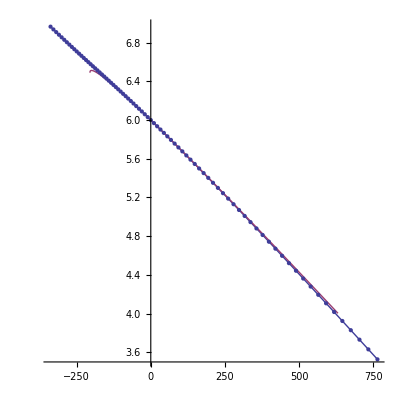

```mathematica
Show[
{ParametricPlot[{
{X[0,0,0,0,GMC δ]1000,LL[0,0,0,0,GMC δ]+6},
{x2[0,0,0,0,GMC δ]1000,L2[0,0,0,0,GMC δ]+6}
},{δ,-0.4,0.4},AspectRatio->1],
Plot[p0+p1 x+p2 x^2+p3 x^3, {x,-300,800},PlotStyle->Green],
ListPlot[DataXL]
}]
```

```mathematica
Remove[q0,q1,q2,q3]
tempData=DataXδ;
{j0,j1,j2}={q0,q1,q2}/.FindFit[tempData,q0+ q1 x+q2 x^2,{q0,q1,q2},x]
{p0,p1,p2,p3}={q0,q1,q2,q3}/.FindFit[tempData,q0+ q1 x+q2 x^2+q3 x^3 ,{q0,q1,q2,q3},x]
Sum[h=tempData[[i,1]];((tempData[[i,2]])-(j0+j1 h +j2 h^2))^2,{i,1,Length[tempData]}]
Sum[h=tempData[[i,1]];((tempData[[i,2]])-(p0+p1 h +p2 h^2+p3 h^3))^2,{i,1,Length[tempData]}]
```

{0.0126163,-0.000961258,6.01718×10^-7}

{0.00613442,-0.000936409,7.68982×10^-7,-3.02366×10^-10}

0.00759925

0.00298447

```mathematica
1/p1
```

-1067.91

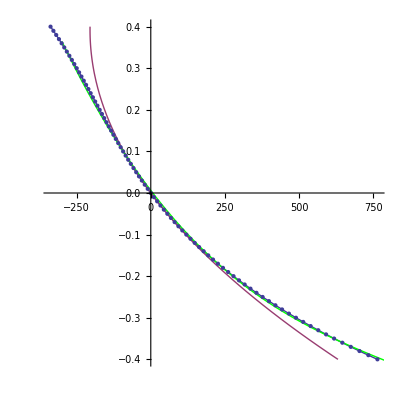

```mathematica
Show[
{ParametricPlot[{
{X[0,0,0,0,GMC δ]1000, δ},
{x2[0,0,0,0,GMC δ]1000,δ}
},{δ,-0.4,0.4},AspectRatio->1],
Plot[p0+p1 x+p2 x^2+p3 x^3, {x,-300,800},PlotStyle->Green],
ListPlot[tempData]
}]
```

```mathematica
Remove[q0,q1,q2,q3]
tempData=DataXA;
{j0,j1,j2}={q0,q1,q2}/.FindFit[tempData,q0+ q1 x+q2 x^2,{q0,q1,q2},x]
{p0,p1,p2,p3}={q0,q1,q2,q3}/.FindFit[tempData,q0+ q1 x+q2 x^2+q3 x^3 ,{q0,q1,q2,q3},x]
Sum[h=tempData[[i,1]];((tempData[[i,2]])-(j0+j1 h +j2 h^2))^2,{i,1,Length[tempData]}]
Sum[h=tempData[[i,1]];((tempData[[i,2]])-(p0+p1 h +p2 h^2+p3 h^3))^2,{i,1,Length[tempData]}]
```

{-0.0052705,0.000463923,-2.37728×10^-7}

{-0.00220778,0.000452182,-3.16761×10^-7,1.4287×10^-10}

0.00138734

0.000357031

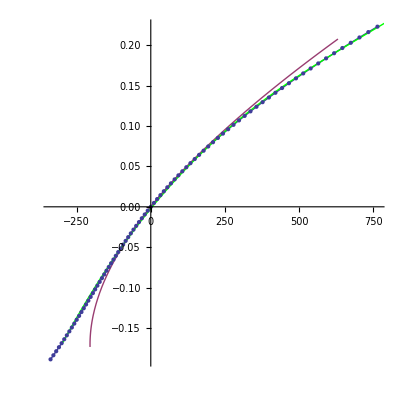

```mathematica
Show[
{ParametricPlot[{
{X[0,0,0,0,GMC δ]1000, A[0,0,0,0,GMC δ]},
{x2[0,0,0,0,GMC δ]1000,a2[0,0,0,0,GMC δ]}
},{δ,-0.4,0.4},AspectRatio->1],
Plot[p0+p1 x+p2 x^2+p3 x^3, {x,-300,800},PlotStyle->Green],
ListPlot[tempData]
}]
```